## Download the data

```mathematica
URL["https://www.census.gov/govs/state/"]
```

URL[https://www.census.gov/govs/state/]

## Import the data

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/aarone/Desktop/state_lotteries

```mathematica
FileNames[]
```

{2015_lottery_table.xls,.DS_Store,.~lock.2015_lottery_table.xls#,scrape.nb}

```mathematica
data0=Import["2015_lottery_table.xls","Data"][[1]]
```

{{Income and Apportionment of State-Administered Lottery Funds: 2015,,,,},{,,,,},{(Thousand dollars),,,,},{,,,,},{,,,,},{,Income,,,},{,(ticket sales,*************Apportionment of funds**************,,},{State,excluding,,,Proceeds},{,commissions),Prizes,Administration,available},{,===============,===============,===============,===============},{,,,,},{United States,6.6788×10^7,4.22789×10^7,3.18017×10^6,2.13628×10^7},{,,,,},{Alabama,-,-,-,-},{Alaska,-,-,-,-},{Arizona,698969.,486638.,41994.,170337.},{Arkansas,385409.,280466.,32989.,71954.},{California,5.52485×10^6,3.50175×10^6,270567.,1.75254×10^6},{,,,,},{Colorado,498210.,331499.,40043.,126668.},{Connecticut,1.0797×10^6,707735.,44060.,327908.},{Delaware,400647.,108964.,50942.,240741.},{Florida,5.27774×10^6,3.62794×10^6,156890.,1.49291×10^6},{Georgia,3.67401×10^6,2.52887×10^6,164678.,980465.},{,,,,},{Hawaii,-,-,-,-},{Idaho,193831.,136769.,11118.,45944.},{Illinois,2.83781×10^6,1.81748×10^6,308686.,711641.},{Indiana,970535.,670980.,143348.,156207.},{Iowa,324767.,196882.,51525.,76360.},{,,,,},{Kansas,231272.,138741.,23429.,69102.},{Kentucky,831073.,556276.,41419.,233378.},{Louisiana,427181.,239198.,25769.,162214.},{Maine,236179.,166667.,14165.,89133.},{Maryland,2.13149×10^6,1.05149×10^6,85581.,994427.},{,,,,},{Massachusetts,5.00564×10^6,3.64135×10^6,100590.,1.26369×10^6},{Michigan,2.52571×10^6,1.69698×10^6,73135.,755598.},{Minnesota,514022.,351668.,25036.,137318.},{Mississippi,-,-,-,-},{Missouri,1.10701×10^6,755429.,46746.,304838.},{,,,,},{Montana,55451.,29256.,8227.,17968.},{Nebraska,149743.,94696.,18357.,36690.},{Nevada,-,-,-,-},{New Hampshire,281133.,176415.,16005.,88713.},{New Jersey,2.83108×10^6,1.8733×10^6,119337.,838443.},{,,,,},{New Mexico,137017.,75592.,20418.,41007.},{New York,7.87377×10^6,4.39685×10^6,374262.,3.10265×10^6},{North Carolina,1.83445×10^6,1.23123×10^6,81448.,521772.},{North Dakota,25841.,13978.,5011.,6852.},{Ohio,2.7128×10^6,1.87526×10^6,122226.,715318.},{,,,,},{Oklahoma,171634.,87783.,24053.,59798.},{Oregon,901728.,211444.,77975.,612309.},{Pennsylvania,3.54661×10^6,2.41165×10^6,39998.,1.09496×10^6},{Rhode Island,542736.,150063.,10076.,382597.},{South Carolina,1.30283×10^6,924137.,38827.,339861.},{,,,,},{South Dakota,147933.,29744.,7753.,110436.},{Tennessee,1.37899×10^6,774250.,59145.,545592.},{Texas,4.28114×10^6,2.85832×10^6,191129.,1.23169×10^6},{Utah,-,-,-,-},{Vermont,104861.,72710.,9228.,22923.},{,,,,},{Virginia,1.73996×10^6,1.11663×10^6,87638.,535696.},{Washington,658854.,432901.,45142.,180811.},{West Virginia,658793.,106476.,32308.,520009.},{Wisconsin,574631.,342441.,38900.,193290.},{Wyoming,-,-,-,-},{,,,,},{,,,,},{,,,,},{Note: A dash ( - ) indicates that the state government did not administer a lottery program.,,,,},{,,,,},{Created: May 11, 2017,,,,},{Last Revised:       May 11, 2017,,,,}}

```mathematica
Dimensions[data0]
```

{79,5}

```mathematica
Grid[data0,Frame->All,Alignment->Left]
```

Income and Apportionment of State-Administered Lottery Funds: 2015 |  |  |  | 
 |  |  |  | 
(Thousand dollars) |  |  |  | 
 |  |  |  | 
 |  |  |  | 
 | Income |  |  | 
 | (ticket sales | *************Apportionment of funds************** |  | 
State | excluding |  |  | Proceeds
 | commissions) | Prizes | Administration | available
 | =============== | =============== | =============== | ===============
 |  |  |  | 
United States | 6.6788×10^7 | 4.22789×10^7 | 3.18017×10^6 | 2.13628×10^7
 |  |  |  | 
Alabama | - | - | - | -
Alaska | - | - | - | -
Arizona | 698969. | 486638. | 41994. | 170337.
Arkansas | 385409. | 280466. | 32989. | 71954.
California | 5.52485×10^6 | 3.50175×10^6 | 270567. | 1.75254×10^6
 |  |  |  | 
Colorado | 498210. | 331499. | 40043. | 126668.
Connecticut | 1.0797×10^6 | 707735. | 44060. | 327908.
Delaware | 400647. | 108964. | 50942. | 240741.
Florida | 5.27774×10^6 | 3.62794×10^6 | 156890. | 1.49291×10^6
Georgia | 3.67401×10^6 | 2.52887×10^6 | 164678. | 980465.
 |  |  |  | 
Hawaii | - | - | - | -
Idaho | 193831. | 136769. | 11118. | 45944.
Illinois | 2.83781×10^6 | 1.81748×10^6 | 308686. | 711641.
Indiana | 970535. | 670980. | 143348. | 156207.
Iowa | 324767. | 196882. | 51525. | 76360.
 |  |  |  | 
Kansas | 231272. | 138741. | 23429. | 69102.
Kentucky | 831073. | 556276. | 41419. | 233378.
Louisiana | 427181. | 239198. | 25769. | 162214.
Maine | 236179. | 166667. | 14165. | 89133.
Maryland | 2.13149×10^6 | 1.05149×10^6 | 85581. | 994427.
 |  |  |  | 
Massachusetts | 5.00564×10^6 | 3.64135×10^6 | 100590. | 1.26369×10^6
Michigan | 2.52571×10^6 | 1.69698×10^6 | 73135. | 755598.
Minnesota | 514022. | 351668. | 25036. | 137318.
Mississippi | - | - | - | -
Missouri | 1.10701×10^6 | 755429. | 46746. | 304838.
 |  |  |  | 
Montana | 55451. | 29256. | 8227. | 17968.
Nebraska | 149743. | 94696. | 18357. | 36690.
Nevada | - | - | - | -
New Hampshire | 281133. | 176415. | 16005. | 88713.
New Jersey | 2.83108×10^6 | 1.8733×10^6 | 119337. | 838443.
 |  |  |  | 
New Mexico | 137017. | 75592. | 20418. | 41007.
New York | 7.87377×10^6 | 4.39685×10^6 | 374262. | 3.10265×10^6
North Carolina | 1.83445×10^6 | 1.23123×10^6 | 81448. | 521772.
North Dakota | 25841. | 13978. | 5011. | 6852.
Ohio | 2.7128×10^6 | 1.87526×10^6 | 122226. | 715318.
 |  |  |  | 
Oklahoma | 171634. | 87783. | 24053. | 59798.
Oregon | 901728. | 211444. | 77975. | 612309.
Pennsylvania | 3.54661×10^6 | 2.41165×10^6 | 39998. | 1.09496×10^6
Rhode Island | 542736. | 150063. | 10076. | 382597.
South Carolina | 1.30283×10^6 | 924137. | 38827. | 339861.
 |  |  |  | 
South Dakota | 147933. | 29744. | 7753. | 110436.
Tennessee | 1.37899×10^6 | 774250. | 59145. | 545592.
Texas | 4.28114×10^6 | 2.85832×10^6 | 191129. | 1.23169×10^6
Utah | - | - | - | -
Vermont | 104861. | 72710. | 9228. | 22923.
 |  |  |  | 
Virginia | 1.73996×10^6 | 1.11663×10^6 | 87638. | 535696.
Washington | 658854. | 432901. | 45142. | 180811.
West Virginia | 658793. | 106476. | 32308. | 520009.
Wisconsin | 574631. | 342441. | 38900. | 193290.
Wyoming | - | - | - | -
 |  |  |  | 
 |  |  |  | 
 |  |  |  | 
Note: A dash ( - ) indicates that the state government did not administer a lottery program. |  |  |  | 
 |  |  |  | 
Created: May 11, 2017 |  |  |  | 
Last Revised:       May 11, 2017 |  |  |  |

## Get the portion of the data we want

```mathematica
data1=DeleteCases[First@SequenceCases[data0,{{"Alabama","-","-","-","-"},___,{"Wyoming","-","-","-","-"}}],{"","","","",""}]
```

{{Alabama,-,-,-,-},{Alaska,-,-,-,-},{Arizona,698969.,486638.,41994.,170337.},{Arkansas,385409.,280466.,32989.,71954.},{California,5.52485×10^6,3.50175×10^6,270567.,1.75254×10^6},{Colorado,498210.,331499.,40043.,126668.},{Connecticut,1.0797×10^6,707735.,44060.,327908.},{Delaware,400647.,108964.,50942.,240741.},{Florida,5.27774×10^6,3.62794×10^6,156890.,1.49291×10^6},{Georgia,3.67401×10^6,2.52887×10^6,164678.,980465.},{Hawaii,-,-,-,-},{Idaho,193831.,136769.,11118.,45944.},{Illinois,2.83781×10^6,1.81748×10^6,308686.,711641.},{Indiana,970535.,670980.,143348.,156207.},{Iowa,324767.,196882.,51525.,76360.},{Kansas,231272.,138741.,23429.,69102.},{Kentucky,831073.,556276.,41419.,233378.},{Louisiana,427181.,239198.,25769.,162214.},{Maine,236179.,166667.,14165.,89133.},{Maryland,2.13149×10^6,1.05149×10^6,85581.,994427.},{Massachusetts,5.00564×10^6,3.64135×10^6,100590.,1.26369×10^6},{Michigan,2.52571×10^6,1.69698×10^6,73135.,755598.},{Minnesota,514022.,351668.,25036.,137318.},{Mississippi,-,-,-,-},{Missouri,1.10701×10^6,755429.,46746.,304838.},{Montana,55451.,29256.,8227.,17968.},{Nebraska,149743.,94696.,18357.,36690.},{Nevada,-,-,-,-},{New Hampshire,281133.,176415.,16005.,88713.},{New Jersey,2.83108×10^6,1.8733×10^6,119337.,838443.},{New Mexico,137017.,75592.,20418.,41007.},{New York,7.87377×10^6,4.39685×10^6,374262.,3.10265×10^6},{North Carolina,1.83445×10^6,1.23123×10^6,81448.,521772.},{North Dakota,25841.,13978.,5011.,6852.},{Ohio,2.7128×10^6,1.87526×10^6,122226.,715318.},{Oklahoma,171634.,87783.,24053.,59798.},{Oregon,901728.,211444.,77975.,612309.},{Pennsylvania,3.54661×10^6,2.41165×10^6,39998.,1.09496×10^6},{Rhode Island,542736.,150063.,10076.,382597.},{South Carolina,1.30283×10^6,924137.,38827.,339861.},{South Dakota,147933.,29744.,7753.,110436.},{Tennessee,1.37899×10^6,774250.,59145.,545592.},{Texas,4.28114×10^6,2.85832×10^6,191129.,1.23169×10^6},{Utah,-,-,-,-},{Vermont,104861.,72710.,9228.,22923.},{Virginia,1.73996×10^6,1.11663×10^6,87638.,535696.},{Washington,658854.,432901.,45142.,180811.},{West Virginia,658793.,106476.,32308.,520009.},{Wisconsin,574631.,342441.,38900.,193290.},{Wyoming,-,-,-,-}}

```mathematica
Dimensions@%
```

{50,5}

## Make an association of the data

```mathematica
properties = {"State","Income","Prizes","Administration","ProceedsAvailable"}
```

{State,Income,Prizes,Administration,ProceedsAvailable}

```mathematica
Thread[{1,2,3} -> {"a","b","c"}]
```

{1→a,2→b,3→c}

```mathematica
AssociationThread[{1,2,3} -> {"a","b","c"}]
```

<|1→a,2→b,3→c|>

```mathematica
datassoc0=AssociationThread[properties -> #]&/@data1
```

{<|State→Alabama,Income→-,Prizes→-,Administration→-,ProceedsAvailable→-|>,<|State→Alaska,Income→-,Prizes→-,Administration→-,ProceedsAvailable→-|>,<|State→Arizona,Income→698969.,Prizes→486638.,Administration→41994.,ProceedsAvailable→170337.|>,<|State→Arkansas,Income→385409.,Prizes→280466.,Administration→32989.,ProceedsAvailable→71954.|>,<|State→California,Income→5.52485×10^6,Prizes→3.50175×10^6,Administration→270567.,ProceedsAvailable→1.75254×10^6|>,<|State→Colorado,Income→498210.,Prizes→331499.,Administration→40043.,ProceedsAvailable→126668.|>,<|State→Connecticut,Income→1.0797×10^6,Prizes→707735.,Administration→44060.,ProceedsAvailable→327908.|>,<|State→Delaware,Income→400647.,Prizes→108964.,Administration→50942.,ProceedsAvailable→240741.|>,<|State→Florida,Income→5.27774×10^6,Prizes→3.62794×10^6,Administration→156890.,ProceedsAvailable→1.49291×10^6|>,<|State→Georgia,Income→3.67401×10^6,Prizes→2.52887×10^6,Administration→164678.,ProceedsAvailable→980465.|>,<|State→Hawaii,Income→-,Prizes→-,Administration→-,ProceedsAvailable→-|>,<|State→Idaho,Income→193831.,Prizes→136769.,Administration→11118.,ProceedsAvailable→45944.|>,<|State→Illinois,Income→2.83781×10^6,Prizes→1.81748×10^6,Administration→308686.,ProceedsAvailable→711641.|>,<|State→Indiana,Income→970535.,Prizes→670980.,Administration→143348.,ProceedsAvailable→156207.|>,<|State→Iowa,Income→324767.,Prizes→196882.,Administration→51525.,ProceedsAvailable→76360.|>,<|State→Kansas,Income→231272.,Prizes→138741.,Administration→23429.,ProceedsAvailable→69102.|>,<|State→Kentucky,Income→831073.,Prizes→556276.,Administration→41419.,ProceedsAvailable→233378.|>,<|State→Louisiana,Income→427181.,Prizes→239198.,Administration→25769.,ProceedsAvailable→162214.|>,<|State→Maine,Income→236179.,Prizes→166667.,Administration→14165.,ProceedsAvailable→89133.|>,<|State→Maryland,Income→2.13149×10^6,Prizes→1.05149×10^6,Administration→85581.,ProceedsAvailable→994427.|>,<|State→Massachusetts,Income→5.00564×10^6,Prizes→3.64135×10^6,Administration→100590.,ProceedsAvailable→1.26369×10^6|>,<|State→Michigan,Income→2.52571×10^6,Prizes→1.69698×10^6,Administration→73135.,ProceedsAvailable→755598.|>,<|State→Minnesota,Income→514022.,Prizes→351668.,Administration→25036.,ProceedsAvailable→137318.|>,<|State→Mississippi,Income→-,Prizes→-,Administration→-,ProceedsAvailable→-|>,<|State→Missouri,Income→1.10701×10^6,Prizes→755429.,Administration→46746.,ProceedsAvailable→304838.|>,<|State→Montana,Income→55451.,Prizes→29256.,Administration→8227.,ProceedsAvailable→17968.|>,<|State→Nebraska,Income→149743.,Prizes→94696.,Administration→18357.,ProceedsAvailable→36690.|>,<|State→Nevada,Income→-,Prizes→-,Administration→-,ProceedsAvailable→-|>,<|State→New Hampshire,Income→281133.,Prizes→176415.,Administration→16005.,ProceedsAvailable→88713.|>,<|State→New Jersey,Income→2.83108×10^6,Prizes→1.8733×10^6,Administration→119337.,ProceedsAvailable→838443.|>,<|State→New Mexico,Income→137017.,Prizes→75592.,Administration→20418.,ProceedsAvailable→41007.|>,<|State→New York,Income→7.87377×10^6,Prizes→4.39685×10^6,Administration→374262.,ProceedsAvailable→3.10265×10^6|>,<|State→North Carolina,Income→1.83445×10^6,Prizes→1.23123×10^6,Administration→81448.,ProceedsAvailable→521772.|>,<|State→North Dakota,Income→25841.,Prizes→13978.,Administration→5011.,ProceedsAvailable→6852.|>,<|State→Ohio,Income→2.7128×10^6,Prizes→1.87526×10^6,Administration→122226.,ProceedsAvailable→715318.|>,<|State→Oklahoma,Income→171634.,Prizes→87783.,Administration→24053.,ProceedsAvailable→59798.|>,<|State→Oregon,Income→901728.,Prizes→211444.,Administration→77975.,ProceedsAvailable→612309.|>,<|State→Pennsylvania,Income→3.54661×10^6,Prizes→2.41165×10^6,Administration→39998.,ProceedsAvailable→1.09496×10^6|>,<|State→Rhode Island,Income→542736.,Prizes→150063.,Administration→10076.,ProceedsAvailable→382597.|>,<|State→South Carolina,Income→1.30283×10^6,Prizes→924137.,Administration→38827.,ProceedsAvailable→339861.|>,<|State→South Dakota,Income→147933.,Prizes→29744.,Administration→7753.,ProceedsAvailable→110436.|>,<|State→Tennessee,Income→1.37899×10^6,Prizes→774250.,Administration→59145.,ProceedsAvailable→545592.|>,<|State→Texas,Income→4.28114×10^6,Prizes→2.85832×10^6,Administration→191129.,ProceedsAvailable→1.23169×10^6|>,<|State→Utah,Income→-,Prizes→-,Administration→-,ProceedsAvailable→-|>,<|State→Vermont,Income→104861.,Prizes→72710.,Administration→9228.,ProceedsAvailable→22923.|>,<|State→Virginia,Income→1.73996×10^6,Prizes→1.11663×10^6,Administration→87638.,ProceedsAvailable→535696.|>,<|State→Washington,Income→658854.,Prizes→432901.,Administration→45142.,ProceedsAvailable→180811.|>,<|State→West Virginia,Income→658793.,Prizes→106476.,Administration→32308.,ProceedsAvailable→520009.|>,<|State→Wisconsin,Income→574631.,Prizes→342441.,Administration→38900.,ProceedsAvailable→193290.|>,<|State→Wyoming,Income→-,Prizes→-,Administration→-,ProceedsAvailable→-|>}

```mathematica
{"Income","Prizes","Administration","ProceedsAvailable"}
```

## Turn numbers into Quantity objects

```mathematica
datassoc0[[All,"Prizes"]]
```

{-,-,486638.,280466.,3.50175×10^6,331499.,707735.,108964.,3.62794×10^6,2.52887×10^6,-,136769.,1.81748×10^6,670980.,196882.,138741.,556276.,239198.,166667.,1.05149×10^6,3.64135×10^6,1.69698×10^6,351668.,-,755429.,29256.,94696.,-,176415.,1.8733×10^6,75592.,4.39685×10^6,1.23123×10^6,13978.,1.87526×10^6,87783.,211444.,2.41165×10^6,150063.,924137.,29744.,774250.,2.85832×10^6,-,72710.,1.11663×10^6,432901.,106476.,342441.,-}

```mathematica
Head/@datassoc0[[All,"Prizes"]]
```

{String,String,Real,Real,Real,Real,Real,Real,Real,Real,String,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,String,Real,Real,Real,String,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,String,Real,Real,Real,Real,Real,String}

```mathematica
Tally[Head/@datassoc0[[All,"Prizes"]]]
```

{{String,7},{Real,43}}

```mathematica
Tally[Head/@datassoc0[[All,"Administration"]]]
```

{{String,7},{Real,43}}

```mathematica
Tally[Head/@datassoc0[[All,"ProceedsAvailable"]]]
```

{{String,7},{Real,43}}

```mathematica
quantitymaker[s_String]:=Missing["NotApplicable"]

quantitymaker[r_Real]:=Quantity[r 1000,"USDollars"]
```

```mathematica
quantitymaker["foo"]
```

Missing[NotApplicable]

```mathematica
quantitymaker[3.14]
```

3 140.00 $

```mathematica
testrec=RandomChoice[datassoc0]
```

<|State→Oregon,Income→901728.,Prizes→211444.,Administration→77975.,ProceedsAvailable→612309.|>

```mathematica
testrec["Income"] = quantitymaker[testrec["Income"]];
```

```mathematica
testrec
```

<|State→Oregon,Income→9.01728e8 $,Prizes→211444.,Administration→77975.,ProceedsAvailable→612309.|>

```mathematica
datassoc1=Module[{rec = #},
(rec[#]=quantitymaker[rec[#]])&/@{"Income","Prizes","Administration","ProceedsAvailable"};
rec]&/@datassoc0;
```

## Turn states into Entity objects

```mathematica
datassoc1//RandomChoice
```

<|State→Wyoming,Income→Missing[NotApplicable],Prizes→Missing[NotApplicable],Administration→Missing[NotApplicable],ProceedsAvailable→Missing[NotApplicable]|>

```mathematica
Interpreter["AdministrativeDivision"][{"Wyoming","Indiana"}]
```

{Wyoming, United States,Indiana, United States}

```mathematica
states = datassoc1[[All,"State"]]
```

```mathematica
{"Alabama","Alaska","Arizona","Arkansas","California","Colorado","Connecticut","Delaware","Florida","Georgia","Hawaii","Idaho","Illinois","Indiana","Iowa","Kansas","Kentucky","Louisiana","Maine","Maryland","Massachusetts","Michigan","Minnesota","Mississippi","Missouri","Montana","Nebraska","Nevada","New Hampshire","New Jersey","New Mexico","New York","North Carolina","North Dakota","Ohio","Oklahoma","Oregon","Pennsylvania","Rhode Island","South Carolina","South Dakota","Tennessee","Texas","Utah","Vermont","Virginia","Washington","West Virginia","Wisconsin","Wyoming"}
```

```mathematica
Length[states]
```

50

```mathematica
stateassoc = AssociationThread[states -> Interpreter["AdministrativeDivision"][states]];
```

```mathematica
Tally[Head/@stateassoc]
```

{{Entity,50}}

```mathematica
datassoc2=Module[{rec = #},
rec["State"]= stateassoc[rec["State"]];
rec
]&/@datassoc1;
```

## Make a Dataset

```mathematica
ds = Dataset[datassoc2]
```

Dataset[<>]

## Put the Dataset into the cloud

```mathematica
CloudPut[ds,Permissions->"Public"]
```

CloudObject[]

## Some visualizations

```mathematica
Normal@ds[[All,"State"]]
```

{Alabama, United States,Alaska, United States,Arizona, United States,Arkansas, United States,California, United States,Colorado, United States,Connecticut, United States,Delaware, United States,Florida, United States,Georgia, United States,Hawaii, United States,Idaho, United States,Illinois, United States,Indiana, United States,Iowa, United States,Kansas, United States,Kentucky, United States,Louisiana, United States,Maine, United States,Maryland, United States,Massachusetts, United States,Michigan, United States,Minnesota, United States,Mississippi, United States,Missouri, United States,Montana, United States,Nebraska, United States,Nevada, United States,New Hampshire, United States,New Jersey, United States,New Mexico, United States,New York, United States,North Carolina, United States,North Dakota, United States,Ohio, United States,Oklahoma, United States,Oregon, United States,Pennsylvania, United States,Rhode Island, United States,South Carolina, United States,South Dakota, United States,Tennessee, United States,Texas, United States,Utah, United States,Vermont, United States,Virginia, United States,Washington, United States,West Virginia, United States,Wisconsin, United States,Wyoming, United States}

```mathematica
DeleteMissing@AssociationThread[Normal@ds[[All,"State"]] ->Normal@ds[[All,"Income"]]]
```

<|Arizona, United States→6.98969e8 $,Arkansas, United States→3.85409e8 $,California, United States→5.524851e9 $,Colorado, United States→4.9821e8 $,Connecticut, United States→1.079703e9 $,Delaware, United States→4.00647e8 $,Florida, United States→5.277739e9 $,Georgia, United States→3.674014e9 $,Idaho, United States→1.93831e8 $,Illinois, United States→2.837805e9 $,Indiana, United States→9.70535e8 $,Iowa, United States→3.24767e8 $,Kansas, United States→2.31272e8 $,Kentucky, United States→8.31073e8 $,Louisiana, United States→4.27181e8 $,Maine, United States→2.36179e8 $,Maryland, United States→2.131494e9 $,Massachusetts, United States→5.005635e9 $,Michigan, United States→2.525711e9 $,Minnesota, United States→5.14022e8 $,Missouri, United States→1.107013e9 $,Montana, United States→5.5451e7 $,Nebraska, United States→1.49743e8 $,New Hampshire, United States→2.81133e8 $,New Jersey, United States→2.831083e9 $,New Mexico, United States→1.37017e8 $,New York, United States→7.873768e9 $,North Carolina, United States→1.834453e9 $,North Dakota, United States→2.5841e7 $,Ohio, United States→2.712802e9 $,Oklahoma, United States→1.71634e8 $,Oregon, United States→9.01728e8 $,Pennsylvania, United States→3.546607e9 $,Rhode Island, United States→5.42736e8 $,South Carolina, United States→1.302825e9 $,South Dakota, United States→1.47933e8 $,Tennessee, United States→1.378987e9 $,Texas, United States→4.281136e9 $,Vermont, United States→1.04861e8 $,Virginia, United States→1.739959e9 $,Washington, United States→6.58854e8 $,West Virginia, United States→6.58793e8 $,Wisconsin, United States→5.74631e8 $|>

```mathematica
GeoRegionValuePlot[DeleteMissing@AssociationThread[Normal@ds[[All,"State"]] ->Normal@ds[[All,"Income"]]]]
```

-Graphics-

```mathematica
Normal@ds[[All,"State"]]//First
```

```mathematica
EntityValue[Normal@ds[[All,"State"]],"Population"]
```

{4849377 people,736732 people,6731484 people,2966369 people,38802500 people,5355866 people,3596677 people,935614 people,19893297 people,10097343 people,1419561 people,1634464 people,12880580 people,6596855 people,3107126 people,2904021 people,4413457 people,4649676 people,1330089 people,5976407 people,6745408 people,9909877 people,5457173 people,2994079 people,6063589 people,1023579 people,1881503 people,2839099 people,1326813 people,8938175 people,2085572 people,19746227 people,9943964 people,739482 people,11594163 people,3878051 people,3970239 people,12787209 people,1055173 people,4832482 people,853175 people,6549352 people,26956958 people,2942902 people,626562 people,8326289 people,7061530 people,1850326 people,5757564 people,584153 people}

```mathematica
GeoRegionValuePlot[Module[{states = Normal@ds[[All,"State"]],populations,prizes = Normal@ds[[All,"Prizes"]]},
populations= EntityValue[states,"Population"];
If[MatchQ[Last@#,_Missing],Nothing,First@# -> N[(Last@#/#[[2]])]]&/@
Transpose[{states,populations,prizes}]]]
```

-Graphics-

```mathematica
GeoRegionValuePlot[Module[{states = Normal@ds[[All,"State"]],populations,prizes = Normal@ds[[All,"Income"]]},
populations= EntityValue[states,"Population"];
If[MatchQ[Last@#,_Missing],Nothing,First@# -> N[(Last@#/#[[2]])]]&/@
Transpose[{states,populations,prizes}]]]
```

-Graphics-

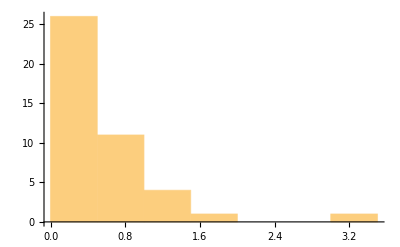

```mathematica
Histogram[Normal@ds[[All,"ProceedsAvailable"]]]
```